This version uses the ``order 0’’ (in the paper) term

```mathematica
$PlotTheme="Scientific";
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};DefaultBaseStyle->texStyle;
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
k1v={k1,0,0};
```

```mathematica
k2v={k2*cth,k2*√(1-cth^2),0};
```

```mathematica
k0v={k0*cpsi,k0*√(1-cpsi^2)*Cos[ϕ],k0*√(1-cpsi^2)*Sin[ϕ]};
```

```mathematica
k01v=k0v+k1v;k12v=k1v+k2v;
```

```mathematica
vel={vx,vy,vz};
```

```mathematica
pretermvelocity=-(ⅈ*k12v.vel)/(4*k12v.k12v)*((k01v.vel*(5*k01v.k01v-2*(k01v.vel)^2)*k01v)/(k01v.k01v))+(k12v.vel)^2/(4*k12v.k12v)*(-(ⅈ*(6*(k01v.vel)^2-7*k01v.k01v)*k01v)/(4*k01v.k01v))+(ⅈ(k12v.vel)^3)/(4*k12v.k12v)*(((k01v.vel)*k01v)/(k01v.k01v))-(ⅈ(k12v.vel))/(24*(k1v.k1v)*(k12v.k12v))*(-30*(k1v.k1v)*(k1v.k12v)+12*(k1v.k1v)^2+31*(k1v.k1v)*(k12v.k12v)+8(k1v.k12v)^2)*(((k01v.vel)*k01v)/(k01v.k01v))-(k12v.vel)^4/(4*(k12v.k12v))*((ⅈ*k01v)/(2*k01v.k01v))+(k12v.vel)^2/(12*(k1v.k1v)*(k12v.k12v))*(4(k1v.k12v)^2+20*(k1v.k1v)*(k12v.k12v)-15*(k1v.k12v)*(k1v.k1v)+6*(k1v.k1v)^2)*((ⅈ*k01v)/(2*k01v.k01v));
```

```mathematica
Length[pretermvelocity]
```

3

```mathematica
preterm=Expectation[pretermvelocity,vel\[Distributed]MultinormalDistribution[{0,0,0},IdentityMatrix[3]]];
```

```mathematica
term=FullSimplify[-ⅈ*(k2v.preterm)/(k2v.k2v)]
```

-((3 cth k1 (cpsi k0+k1) (-4 cpsi k0^3+(-5+4 cpsi^2) k0^2 k1+12 cpsi k0 k1^2+5 k1^3)+3 (2 (-1+cpsi^2+cth^2-3 cpsi^2 cth^2) k0^4+2 cpsi (4-9 cth^2+4 cpsi^2 (-1+3 cth^2)) k0^3 k1+(11-17 cth^2+cpsi^2 (-11+69 cth^2)) k0^2 k1^2+52 cpsi cth^2 k0 k1^3+10 cth^2 k1^4) k2+cth (3 cpsi (17-18 cth^2+6 cpsi^2 (-3+5 cth^2)) k0^3+(63-66 cth^2+cpsi^2 (-46+214 cth^2)) k0^2 k1+3 cpsi (3+40 cth^2) k0 k1^2+(-11+8 cth^2) k1^3) k2^2+((13+8 cth^2) (1-cpsi^2+(-1+3 cpsi^2) cth^2) k0^2+2 cpsi cth^2 (-11+8 cth^2) k0 k1-48 cth^2 k1^2) k2^3-2 cth (11+4 cth^2) (cpsi k0+k1) k2^4+√(1-cpsi^2) √(1-cth^2) k0 (3 k1 (-4 cpsi k0^3+(-5+4 cpsi^2) k0^2 k1+12 cpsi k0 k1^2+5 k1^3)+6 cth (-4 cpsi k0^3+(-5+16 cpsi^2) k0^2 k1+40 cpsi k0 k1^2+16 k1^3) k2+(3 (8-9 cpsi^2+9 (-1+5 cpsi^2) cth^2) k0^2+20 cpsi (1+14 cth^2) k0 k1+(-11+104 cth^2) k1^2) k2^2+2 cth (2 cpsi (13+8 cth^2) k0+(-11+8 cth^2) k1) k2^3-2 (11+4 cth^2) k2^4) Cos[ϕ]+(-1+cpsi^2) (-1+cth^2) k0^2 k2 (-6 k0^2+33 k1^2+66 cth k1 k2+(13+8 cth^2) k2^2+6 cpsi k0 (4 k1+9 cth k2)) Cos[2 ϕ]+9 (1-cpsi^2)^(3/2) (1-cth^2)^(3/2) k0^3 k2^2 Cos[3 ϕ])/(48 (k0^2+2 cpsi k0 k1+k1^2) k2 (k1^2+2 cth k1 k2+k2^2)))

```mathematica
test=Simplify[term/.k0->0]
```

(cth (-15 k1^4-30 cth k1^3 k2+(11-8 cth^2) k1^2 k2^2+48 cth k1 k2^3+2 (11+4 cth^2) k2^4))/(48 k1 k2 (k1^2+2 cth k1 k2+k2^2))

The following comes from ``2017-04-08 Big integration - with comparison use of expectations.nb’’

```mathematica
dimlessprod1=-(ⅈ cth (15 k1^4+30 cth k1^3 k2-11 k1^2 k2^2+8 cth^2 k1^2 k2^2-48 cth k1 k2^3-22 k2^4-8 cth^2 k2^4))/(48 k1 k2 (k1^2+2 cth k1 k2+k2^2));
```

```mathematica
dimlessprod1mult=(-ⅈ)*dimlessprod1;
```

The following line checks for consistency with  ``2017-04-08 Big integration - with comparison use of expectations.nb’’, 0 being consistent

```mathematica
FullSimplify[test-dimlessprod1mult]
```

0

Note that in the next function the divisor is 2*π^2, not 16*π^2 as in the leading order (because the factor of 8 came from the leading order equivalenet of term).  The division by 2*π^2 is done after the integration.  In the integrand, the simplification k0^2*k1^2*k2^2*r^2*Sin[r*k0]/(r*k0)=k0*k1^2*k2^2*r*Sin[r*k0] has been made.

```mathematica
inter[r_]:=Module[{int,errors},int=Chop[NIntegrate[Boole[(k1^2+k2^2+2*k1*k2*cth≤1)&&(k1^2+k0^2+2*k1*k0*cpsi≤1)]*k0*k1^2*k2^2*r*Sin[r*k0]*term,{k1,0,2},{k2,0,1},{k0,0,3},{ϕ,0,2*π},{cth,-1,1},{cpsi,-1,1},PrecisionGoal->5,(*WorkingPrecision->15,*)IntegrationMonitor:>((errors=Through[#1@"Error"])&)]];
{{r,int/(2*π^2)},Re[Total@errors]/(2*π^2),Abs[Re[Total@errors]/Re[int]]}]
```

```mathematica
taberr=<<"2017-05-29 New distribution over space 20ths zeroth order.m";
```

```mathematica
(*taberr={};Monitor[For[r=1/20,r≤15,r=r+1/20,taberr=Join[taberr,{inter[r]}]],taberr//MatrixForm//ScientificForm];taberr//MatrixForm//ScientificForm*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000336663 and 2.27907×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000135796 and 9.07159×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000309852 and 0.0000201987 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

({1/20,-1.70555×10^-6} | 1.15459×10^-7 | 6.7696×10^-2
{1/10,-6.87951×10^-6} | 4.59572×10^-7 | 6.6803×10^-2
{3/20,-1.56973×10^-5} | 1.02328×10^-6 | 6.51884×10^-2
{1/5,-2.84359×10^-5} | 1.80382×10^-6 | 6.34348×10^-2
{1/4,-4.54949×10^-5} | 2.77823×10^-6 | 6.10668×10^-2
{3/10,-6.7364×10^-5} | 3.90633×10^-6 | 5.79884×10^-2
{7/20,-9.45229×10^-5} | 5.37185×10^-6 | 5.68312×10^-2
{2/5,-1.27751×10^-4} | 6.96063×10^-6 | 5.44857×10^-2
{9/20,-1.67238×10^-4} | 8.89293×10^-6 | 5.31752×10^-2
{1/2,-2.14596×10^-4} | 1.11693×10^-5 | 5.20482×10^-2
{11/20,-2.7015×10^-4} | 1.31479×10^-5 | 4.86688×10^-2
{3/5,-3.34889×10^-4} | 1.56687×10^-5 | 4.67877×10^-2
{13/20,-4.09754×10^-4} | 1.83098×10^-5 | 4.46849×10^-2
{7/10,-4.95429×10^-4} | 2.06958×10^-5 | 4.17736×10^-2
{3/4,-5.94134×10^-4} | 2.27254×10^-5 | 3.82496×10^-2
{4/5,-7.04383×10^-4} | 2.57194×10^-5 | 3.65133×10^-2
{17/20,-8.25672×10^-4} | 2.92405×10^-5 | 3.54142×10^-2
{9/10,-9.6283×10^-4} | 3.28587×10^-5 | 3.41271×10^-2
{19/20,-1.1139×10^-3} | 3.53037×10^-5 | 3.16936×10^-2
{1,-1.2782×10^-3} | 3.71966×10^-5 | 2.91007×10^-2
{21/20,-1.46125×10^-3} | 4.11679×10^-5 | 2.81731×10^-2
{11/10,-1.65777×10^-3} | 4.48207×10^-5 | 2.70368×10^-2
{23/20,-1.87004×10^-3} | 4.72155×10^-5 | 2.52484×10^-2
{6/5,-2.09647×10^-3} | 5.08122×10^-5 | 2.4237×10^-2
{5/4,-2.33769×10^-3} | 5.2835×10^-5 | 2.26014×10^-2
{13/10,-2.59386×10^-3} | 5.57962×10^-5 | 2.15108×10^-2
{27/20,-2.86476×10^-3} | 5.83431×10^-5 | 2.03658×10^-2
{7/5,-3.14554×10^-3} | 6.13902×10^-5 | 1.95166×10^-2
{29/20,-3.43914×10^-3} | 6.494×10^-5 | 1.88826×10^-2
{3/2,-3.74409×10^-3} | 6.80931×10^-5 | 1.81869×10^-2
{31/20,-4.0589×10^-3} | 7.01636×10^-5 | 1.72864×10^-2
{8/5,-4.38134×10^-3} | 7.44282×10^-5 | 1.69875×10^-2
{33/20,-4.71563×10^-3} | 7.6283×10^-5 | 1.61766×10^-2
{17/10,-5.0515×10^-3} | 8.03386×10^-5 | 1.59039×10^-2
{7/4,-5.38848×10^-3} | 7.90741×10^-5 | 1.46747×10^-2
{9/5,-5.72614×10^-3} | 8.07802×10^-5 | 1.41073×10^-2
{37/20,-6.0655×10^-3} | 8.0386×10^-5 | 1.3253×10^-2
{19/10,-6.39801×10^-3} | 8.09496×10^-5 | 1.26523×10^-2
{39/20,-6.72306×10^-3} | 8.51853×10^-5 | 1.26706×10^-2
{2,-7.04458×10^-3} | 8.97854×10^-5 | 1.27453×10^-2
{41/20,-7.35779×10^-3} | 9.24407×10^-5 | 1.25636×10^-2
{21/10,-7.65186×10^-3} | 9.58002×10^-5 | 1.25199×10^-2
{43/20,-7.93401×10^-3} | 9.98677×10^-5 | 1.25873×10^-2
{11/5,-8.19797×10^-3} | 1.01576×10^-4 | 1.23904×10^-2
{9/4,-8.44459×10^-3} | 1.00321×10^-4 | 1.18799×10^-2
{23/10,-8.66389×10^-3} | 1.00763×10^-4 | 1.16302×10^-2
{47/20,-8.87979×10^-3} | 9.66111×10^-5 | 1.08799×10^-2
{12/5,-9.03941×10^-3} | 1.05674×10^-4 | 1.16904×10^-2
{49/20,-9.19182×10^-3} | 1.05264×10^-4 | 1.1452×10^-2
{5/2,-9.31104×10^-3} | 1.10068×10^-4 | 1.18213×10^-2
{51/20,-9.39595×10^-3} | 1.09679×10^-4 | 1.1673×10^-2
{13/5,-9.45075×10^-3} | 1.0817×10^-4 | 1.14457×10^-2
{53/20,-9.47771×10^-3} | 1.13043×10^-4 | 1.19273×10^-2
{27/10,-9.46976×10^-3} | 1.12263×10^-4 | 1.18549×10^-2
{11/4,-9.42552×10^-3} | 1.13489×10^-4 | 1.20407×10^-2
{14/5,-9.29792×10^-3} | 1.04992×10^-4 | 1.1292×10^-2
{57/20,-9.24985×10^-3} | 1.10779×10^-4 | 1.19763×10^-2
{29/10,-9.09191×10^-3} | 1.13803×10^-4 | 1.2517×10^-2
{59/20,-8.92205×10^-3} | 1.19367×10^-4 | 1.33789×10^-2
{3,-8.71208×10^-3} | 1.15917×10^-4 | 1.33053×10^-2
{61/20,-8.47127×10^-3} | 1.20801×10^-4 | 1.42601×10^-2
{31/10,-8.19151×10^-3} | 1.20957×10^-4 | 1.47661×10^-2
{63/20,-7.88607×10^-3} | 1.22766×10^-4 | 1.55675×10^-2
{16/5,-7.57882×10^-3} | 1.2729×10^-4 | 1.67955×10^-2
{13/4,-7.22513×10^-3} | 1.37329×10^-4 | 1.90071×10^-2
{33/10,-6.85069×10^-3} | 1.36217×10^-4 | 1.98837×10^-2
{67/20,-6.45234×10^-3} | 1.40072×10^-4 | 2.17088×10^-2
{17/5,-6.02816×10^-3} | 1.39735×10^-4 | 2.31804×10^-2
{69/20,-5.59453×10^-3} | 1.42258×10^-4 | 2.54281×10^-2
{7/2,-5.14391×10^-3} | 1.39432×10^-4 | 2.71062×10^-2
{71/20,-4.67474×10^-3} | 1.50897×10^-4 | 3.22793×10^-2
{18/5,-4.20588×10^-3} | 1.51543×10^-4 | 3.60312×10^-2
{73/20,-3.74823×10^-3} | 1.49031×10^-4 | 3.97604×10^-2
{37/10,-3.23907×10^-3} | 1.52887×10^-4 | 4.72009×10^-2
{15/4,-2.75486×10^-3} | 1.57726×10^-4 | 5.72537×10^-2
{19/5,-2.2801×10^-3} | 1.4863×10^-4 | 6.51858×10^-2
{77/20,-1.79672×10^-3} | 1.61771×10^-4 | 9.00369×10^-2
{39/10,-1.33375×10^-3} | 1.63347×10^-4 | 1.22472×10^-1
{79/20,-8.75164×10^-4} | 1.63533×10^-4 | 1.8686×10^-1
{4,-4.02665×10^-4} | 1.76487×10^-4 | 4.38297×10^-1
{81/20,3.6709×10^-5} | 1.74847×10^-4 | 4.76307
{41/10,4.61052×10^-4} | 1.85359×10^-4 | 4.02035×10^-1
{83/20,8.68389×10^-4} | 1.88299×10^-4 | 2.16837×10^-1
{21/5,1.25718×10^-3} | 1.85348×10^-4 | 1.47431×10^-1
{17/4,1.63571×10^-3} | 1.89367×10^-4 | 1.15771×10^-1
{43/10,1.98879×10^-3} | 1.98389×10^-4 | 9.97536×10^-2
{87/20,2.30476×10^-3} | 2.00168×10^-4 | 8.685×10^-2
{22/5,2.60698×10^-3} | 2.02208×10^-4 | 7.75639×10^-2
{89/20,2.89804×10^-3} | 2.01458×10^-4 | 6.95152×10^-2
{9/2,3.12909×10^-3} | 2.06866×10^-4 | 6.61106×10^-2
{91/20,3.35511×10^-3} | 2.07504×10^-4 | 6.18471×10^-2
{23/5,3.539×10^-3} | 2.13215×10^-4 | 6.02474×10^-2
{93/20,3.71244×10^-3} | 2.14341×10^-4 | 5.77357×10^-2
{47/10,3.87008×10^-3} | 2.13473×10^-4 | 5.51598×10^-2
{19/4,3.98349×10^-3} | 2.13499×10^-4 | 5.35959×10^-2
{24/5,4.07247×10^-3} | 2.22274×10^-4 | 5.45796×10^-2
{97/20,4.12784×10^-3} | 2.24925×10^-4 | 5.44897×10^-2
{49/10,4.18673×10^-3} | 2.43481×10^-4 | 5.81555×10^-2
{99/20,4.22324×10^-3} | 2.33376×10^-4 | 5.526×10^-2
{5,4.22082×10^-3} | 2.31687×10^-4 | 5.48916×10^-2
{101/20,4.19156×10^-3} | 2.20531×10^-4 | 5.26131×10^-2
{51/10,4.13553×10^-3} | 2.34892×10^-4 | 5.67985×10^-2
{103/20,4.08144×10^-3} | 2.29721×10^-4 | 5.62843×10^-2
{26/5,3.99899×10^-3} | 2.29498×10^-4 | 5.73889×10^-2
{21/4,3.91058×10^-3} | 2.3742×10^-4 | 6.07124×10^-2
{53/10,3.81109×10^-3} | 2.46995×10^-4 | 6.48094×10^-2
{107/20,3.69492×10^-3} | 2.47883×10^-4 | 6.70875×10^-2
{27/5,3.56145×10^-3} | 2.3898×10^-4 | 6.71018×10^-2
{109/20,3.43511×10^-3} | 2.56278×10^-4 | 7.46056×10^-2
{11/2,3.27528×10^-3} | 2.49323×10^-4 | 7.61227×10^-2
{111/20,3.1262×10^-3} | 2.50479×10^-4 | 8.01224×10^-2
{28/5,2.96927×10^-3} | 2.50058×10^-4 | 8.42155×10^-2
{113/20,2.82556×10^-3} | 2.55255×10^-4 | 9.03378×10^-2
{57/10,2.65487×10^-3} | 2.66762×10^-4 | 1.0048×10^-1
{23/4,2.49056×10^-3} | 2.62415×10^-4 | 1.05364×10^-1
{29/5,2.32321×10^-3} | 2.62405×10^-4 | 1.1295×10^-1
{117/20,2.17274×10^-3} | 2.61825×10^-4 | 1.20504×10^-1
{59/10,1.97794×10^-3} | 2.69516×10^-4 | 1.36261×10^-1
{119/20,1.83532×10^-3} | 2.86105×10^-4 | 1.55888×10^-1
{6,1.6968×10^-3} | 2.86225×10^-4 | 1.68685×10^-1
{121/20,1.55665×10^-3} | 2.97943×10^-4 | 1.914×10^-1
{61/10,1.41383×10^-3} | 2.97633×10^-4 | 2.10516×10^-1
{123/20,1.13918×10^-3} | 2.89567×10^-4 | 2.5419×10^-1
{31/5,1.14682×10^-3} | 3.14159×10^-4 | 2.73938×10^-1
{25/4,1.00795×10^-3} | 3.17703×10^-4 | 3.15197×10^-1
{63/10,9.11107×10^-4} | 3.22652×10^-4 | 3.54132×10^-1
{127/20,7.96644×10^-4} | 3.06189×10^-4 | 3.84348×10^-1
{32/5,6.93747×10^-4} | 3.06841×10^-4 | 4.42295×10^-1
{129/20,5.29267×10^-4} | 2.92741×10^-4 | 5.53106×10^-1
{13/2,5.23449×10^-4} | 3.22959×10^-4 | 6.16983×10^-1
{131/20,4.49169×10^-4} | 3.25296×10^-4 | 7.24217×10^-1
{33/5,3.85598×10^-4} | 3.23994×10^-4 | 8.40238×10^-1
{133/20,3.1329×10^-4} | 3.36063×10^-4 | 1.07269
{67/10,2.95598×10^-4} | 3.00346×10^-4 | 1.01606
{27/4,1.99136×10^-4} | 3.46526×10^-4 | 1.74014
{34/5,1.67212×10^-4} | 3.39374×10^-4 | 2.0296
{137/20,1.21461×10^-4} | 3.51679×10^-4 | 2.89541
{69/10,9.33093×10^-5} | 3.50279×10^-4 | 3.75396
{139/20,6.06336×10^-5} | 3.72536×10^-4 | 6.14405
{7,3.4889×10^-5} | 3.88593×10^-4 | 1.1138×10^1
{141/20,1.65934×10^-5} | 3.81884×10^-4 | 2.30142×10^1
{71/10,-2.43756×10^-8} | 3.71363×10^-4 | 1.5235×10^4
{143/20,-1.3913×10^-5} | 3.9653×10^-4 | 2.85006×10^1
{36/5,-1.84191×10^-5} | 3.83945×10^-4 | 2.0845×10^1
{29/4,-3.77922×10^-5} | 3.90908×10^-4 | 1.03436×10^1
{73/10,-3.58015×10^-5} | 3.95965×10^-4 | 1.106×10^1
{147/20,-3.40736×10^-5} | 3.88849×10^-4 | 1.1412×10^1
{37/5,-2.5913×10^-5} | 4.01427×10^-4 | 1.54914×10^1
{149/20,-2.52294×10^-5} | 4.06817×10^-4 | 1.61247×10^1
{15/2,-4.30548×10^-5} | 4.19055×10^-4 | 9.73307
{151/20,-3.98617×10^-5} | 4.26714×10^-4 | 1.07049×10^1
{38/5,-4.3108×10^-5} | 4.21486×10^-4 | 9.77745
{153/20,-4.41432×10^-5} | 4.27291×10^-4 | 9.67966
{77/10,-3.38108×10^-5} | 4.44745×10^-4 | 1.31539×10^1
{31/4,-2.52954×10^-5} | 4.45448×10^-4 | 1.76099×10^1
{39/5,5.39356×10^-6} | 4.43305×10^-4 | 8.21917×10^1
{157/20,-4.17036×10^-6} | 4.70808×10^-4 | 1.12894×10^2
{79/10,1.90956×10^-5} | 4.82762×10^-4 | 2.52813×10^1
{159/20,1.13934×10^-5} | 4.50841×10^-4 | 3.95704×10^1
{8,4.24701×10^-6} | 4.8187×10^-4 | 1.13461×10^2
{161/20,5.92787×10^-5} | 4.75961×10^-4 | 8.0292
{81/10,3.25697×10^-5} | 4.59951×10^-4 | 1.41221×10^1
{163/20,3.73467×10^-5} | 4.61313×10^-4 | 1.23522×10^1
{41/5,2.07845×10^-5} | 4.7232×10^-4 | 2.27246×10^1
{33/4,3.46089×10^-5} | 4.77257×10^-4 | 1.379×10^1
{83/10,5.14171×10^-5} | 4.78006×10^-4 | 9.29663
{167/20,4.52031×10^-5} | 4.90544×10^-4 | 1.0852×10^1
{42/5,4.06152×10^-5} | 4.71278×10^-4 | 1.16035×10^1
{169/20,5.23923×10^-5} | 4.63195×10^-4 | 8.8409
{17/2,7.42835×10^-5} | 5.12678×10^-4 | 6.90164
{171/20,5.38067×10^-5} | 4.9493×10^-4 | 9.19829
{43/5,7.63835×10^-5} | 4.82276×10^-4 | 6.31387
{173/20,5.04135×10^-5} | 4.46452×10^-4 | 8.8558
{87/10,2.87791×10^-5} | 4.78951×10^-4 | 1.66423×10^1
{35/4,4.49641×10^-5} | 4.97413×10^-4 | 1.10624×10^1
{44/5,3.46715×10^-5} | 5.13417×10^-4 | 1.4808×10^1
{177/20,4.72167×10^-5} | 5.13949×10^-4 | 1.08849×10^1
{89/10,2.79976×10^-5} | 5.36676×10^-4 | 1.91687×10^1
{179/20,4.20039×10^-5} | 5.38375×10^-4 | 1.28173×10^1
{9,3.82902×10^-5} | 5.45781×10^-4 | 1.42538×10^1
{181/20,2.66011×10^-5} | 5.68646×10^-4 | 2.13768×10^1
{91/10,2.18248×10^-5} | 5.50951×10^-4 | 2.52442×10^1
{183/20,1.77358×10^-5} | 5.86103×10^-4 | 3.30462×10^1
{46/5,2.38441×10^-5} | 5.95237×10^-4 | 2.49637×10^1
{37/4,8.48056×10^-6} | 5.80596×10^-4 | 6.8462×10^1
{93/10,1.18436×10^-5} | 6.04507×10^-4 | 5.10407×10^1
{187/20,1.20806×10^-5} | 5.61882×10^-4 | 4.65112×10^1
{47/5,-4.1553×10^-6} | 5.7714×10^-4 | 1.38892×10^2
{189/20,1.27898×10^-5} | 5.90781×10^-4 | 4.61916×10^1
{19/2,-1.51644×10^-5} | 5.80626×10^-4 | 3.82888×10^1
{191/20,-1.09258×10^-5} | 6.17132×10^-4 | 5.64837×10^1
{48/5,-2.13154×10^-5} | 6.00683×10^-4 | 2.81806×10^1
{193/20,-1.81071×10^-5} | 6.09202×10^-4 | 3.36443×10^1
{97/10,-1.01919×10^-4} | 6.25237×10^-4 | 6.13463
{39/4,-2.75056×10^-5} | 6.29732×10^-4 | 2.28947×10^1
{49/5,-5.44548×10^-5} | 6.42687×10^-4 | 1.18022×10^1
{197/20,-3.48057×10^-5} | 6.5086×10^-4 | 1.86998×10^1
{99/10,-5.13681×10^-5} | 6.48142×10^-4 | 1.26176×10^1
{199/20,4.46761×10^-7} | 6.0016×10^-4 | 1.34336×10^3
{10,-4.75661×10^-5} | 6.18733×10^-4 | 1.30079×10^1
{201/20,-5.23203×10^-5} | 6.37156×10^-4 | 1.2178×10^1
{101/10,-3.65673×10^-5} | 6.53998×10^-4 | 1.78848×10^1
{203/20,-4.88869×10^-5} | 6.6152×10^-4 | 1.35316×10^1
{51/5,-6.45204×10^-5} | 6.7612×10^-4 | 1.04792×10^1
{41/4,-6.28819×10^-5} | 6.60818×10^-4 | 1.05089×10^1
{103/10,-6.76997×10^-5} | 6.95854×10^-4 | 1.02785×10^1
{207/20,-7.75762×10^-5} | 7.20179×10^-4 | 9.28351
{52/5,-6.51486×10^-5} | 6.98784×10^-4 | 1.0726×10^1
{209/20,-9.05748×10^-5} | 7.10644×10^-4 | 7.84594
{21/2,-1.09976×10^-4} | 7.25308×10^-4 | 6.59513
{211/20,-9.27007×10^-5} | 7.33726×10^-4 | 7.915
{53/5,-9.5064×10^-5} | 7.26021×10^-4 | 7.63718
{213/20,1.08664×10^-3} | 6.28523×10^-4 | 5.78411×10^-1
{107/10,-7.30465×10^-5} | 6.90685×10^-4 | 9.45543
{43/4,-7.39156×10^-5} | 7.06585×10^-4 | 9.55934
{54/5,-8.03373×10^-5} | 7.14065×10^-4 | 8.88834
{217/20,-7.67787×10^-5} | 7.09165×10^-4 | 9.23647
{109/10,-6.16781×10^-5} | 7.28247×10^-4 | 1.18072×10^1
{219/20,-6.50711×10^-5} | 7.12605×10^-4 | 1.09512×10^1
{11,-7.74315×10^-5} | 7.17546×10^-4 | 9.26684
{221/20,-1.34961×10^-5} | 7.34908×10^-4 | 5.44532×10^1
{111/10,-5.34388×10^-5} | 7.5258×10^-4 | 1.4083×10^1
{223/20,-4.12665×10^-5} | 7.51156×10^-4 | 1.82026×10^1
{56/5,-3.4548×10^-5} | 7.43883×10^-4 | 2.15318×10^1
{45/4,-4.81263×10^-5} | 7.40916×10^-4 | 1.53952×10^1
{113/10,-1.77783×10^-5} | 7.45047×10^-4 | 4.19078×10^1
{227/20,-9.26672×10^-5} | 7.23212×10^-4 | 7.8044
{57/5,-4.3297×10^-5} | 7.5751×10^-4 | 1.74957×10^1
{229/20,7.4289×10^-5} | 7.5052×10^-4 | 1.01027×10^1
{23/2,-1.72067×10^-7} | 7.93088×10^-4 | 4.60917×10^3
{231/20,-8.95476×10^-6} | 8.02389×10^-4 | 8.96047×10^1
{58/5,-9.93724×10^-6} | 8.32171×10^-4 | 8.37427×10^1
{233/20,-1.56508×10^-5} | 8.43929×10^-4 | 5.39224×10^1
{117/10,-1.27469×10^-5} | 7.98598×10^-4 | 6.26506×10^1
{47/4,2.30405×10^-5} | 8.8303×10^-4 | 3.83251×10^1
{59/5,3.93594×10^-6} | 8.97924×10^-4 | 2.28134×10^2
{237/20,8.00533×10^-5} | 8.19849×10^-4 | 1.02413×10^1
{119/10,3.48202×10^-5} | 8.52663×10^-4 | 2.44876×10^1
{239/20,3.84558×10^-5} | 8.88767×10^-4 | 2.31114×10^1
{12,-4.22806×10^-6} | 9.22283×10^-4 | 2.18134×10^2
{241/20,2.3995×10^-5} | 9.18298×10^-4 | 3.82704×10^1
{121/10,-5.53842×10^-6} | 9.1904×10^-4 | 1.65939×10^2
{243/20,2.59822×10^-5} | 9.0889×10^-4 | 3.49812×10^1
{61/5,-2.38416×10^-5} | 8.95621×10^-4 | 3.75655×10^1
{49/4,2.19441×10^-6} | 9.00487×10^-4 | 4.10356×10^2
{123/10,1.44463×10^-5} | 9.23449×10^-4 | 6.39231×10^1
{247/20,1.86869×10^-5} | 9.39417×10^-4 | 5.02714×10^1
{62/5,2.48903×10^-5} | 9.34276×10^-4 | 3.75358×10^1
{249/20,1.7428×10^-5} | 9.45329×10^-4 | 5.42419×10^1
{25/2,6.01475×10^-6} | 9.44348×10^-4 | 1.57005×10^2
{251/20,1.33055×10^-5} | 9.36836×10^-4 | 7.04095×10^1
{63/5,6.51646×10^-5} | 8.7363×10^-4 | 1.34065×10^1
{253/20,2.48097×10^-5} | 9.10202×10^-4 | 3.66874×10^1
{127/10,4.01406×10^-7} | 9.75622×10^-4 | 2.43051×10^3
{51/4,4.67322×10^-6} | 9.80203×10^-4 | 2.09749×10^2
{64/5,2.03505×10^-5} | 9.83942×10^-4 | 4.83497×10^1
{257/20,2.9969×10^-5} | 1.02197×10^-3 | 3.41008×10^1
{129/10,5.90365×10^-5} | 9.89987×10^-4 | 1.67691×10^1
{259/20,2.59929×10^-5} | 9.98249×10^-4 | 3.84047×10^1
{13,-4.6344×10^-6} | 9.99457×10^-4 | 2.1566×10^2
{261/20,6.87748×10^-6} | 9.72802×10^-4 | 1.41447×10^2
{131/10,4.0715×10^-5} | 1.00821×10^-3 | 2.47626×10^1
{263/20,-3.38506×10^-5} | 9.48062×10^-4 | 2.80073×10^1
{66/5,-1.53571×10^-5} | 9.71791×10^-4 | 6.32797×10^1
{53/4,-2.56025×10^-5} | 9.92645×10^-4 | 3.87713×10^1
{133/10,-5.14635×10^-5} | 1.05677×10^-3 | 2.05344×10^1
{267/20,-7.00452×10^-5} | 1.06124×10^-3 | 1.51507×10^1
{67/5,-4.35981×10^-5} | 1.08221×10^-3 | 2.48225×10^1
{269/20,-3.56653×10^-5} | 1.08488×10^-3 | 3.04185×10^1
{27/2,-3.41341×10^-5} | 1.02299×10^-3 | 2.99697×10^1
{271/20,-3.08147×10^-5} | 1.04368×10^-3 | 3.38696×10^1
{68/5,3.37165×10^-6} | 1.01931×10^-3 | 3.02319×10^2
{273/20,-3.2857×10^-5} | 1.07377×10^-3 | 3.26802×10^1
{137/10,-9.7633×10^-5} | 1.0573×10^-3 | 1.08294×10^1
{55/4,-3.68692×10^-5} | 1.1052×10^-3 | 2.99762×10^1
{69/5,-7.56128×10^-5} | 1.12981×10^-3 | 1.4942×10^1
{277/20,-2.58425×10^-5} | 1.07333×10^-3 | 4.15335×10^1
{139/10,-3.49095×10^-5} | 1.08644×10^-3 | 3.11216×10^1
{279/20,5.80325×10^-4} | 1.05052×10^-3 | 1.81023
{14,-1.65902×10^-5} | 1.15933×10^-3 | 6.988×10^1
{281/20,-1.95233×10^-5} | 1.12815×10^-3 | 5.77847×10^1
{141/10,2.4307×10^-6} | 1.16967×10^-3 | 4.81207×10^2
{283/20,-2.92249×10^-5} | 1.23533×10^-3 | 4.22698×10^1
{71/5,-3.65224×10^-5} | 1.25476×10^-3 | 3.43559×10^1
{57/4,-8.15489×10^-5} | 1.12365×10^-3 | 1.37788×10^1
{143/10,-3.5161×10^-5} | 1.26362×10^-3 | 3.59382×10^1
{287/20,-4.79711×10^-7} | 1.26611×10^-3 | 2.63931×10^3
{72/5,1.7457×10^-6} | 1.23851×10^-3 | 7.09465×10^2
{289/20,-1.258×10^-5} | 1.22025×10^-3 | 9.69986×10^1
{29/2,-4.57266×10^-6} | 1.20685×10^-3 | 2.63927×10^2
{291/20,-3.79209×10^-5} | 1.20246×10^-3 | 3.17098×10^1
{73/5,-1.1302×10^-4} | 1.15128×10^-3 | 1.01865×10^1
{293/20,-1.75901×10^-5} | 1.20248×10^-3 | 6.83613×10^1
{147/10,-2.62796×10^-4} | 1.16233×10^-3 | 4.42294
{59/4,-1.68783×10^-4} | 1.22581×10^-3 | 7.26265
{74/5,-7.54607×10^-5} | 1.31218×10^-3 | 1.73889×10^1
{297/20,-7.19838×10^-5} | 1.29846×10^-3 | 1.80382×10^1
{149/10,-5.00762×10^-5} | 1.33938×10^-3 | 2.67469×10^1
{299/20,-7.20709×10^-5} | 1.31104×10^-3 | 1.8191×10^1
{15,-6.43283×10^-5} | 1.29993×10^-3 | 2.02078×10^1)

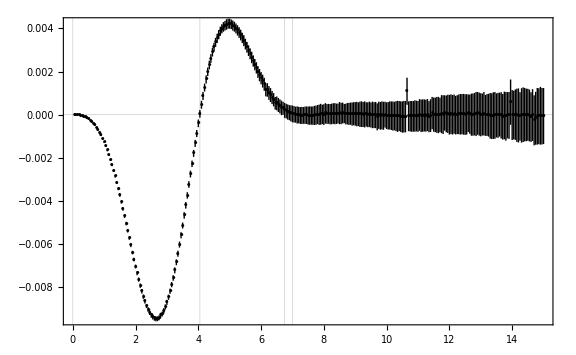

```mathematica
figscgr20thszerothorder=ErrorListPlot[Table[{taberr[[n,1]],ErrorBar[taberr[[n,2]]]},{n,1,Length[taberr]}],GridLines->{{0,4.05,6.75,7},{0}},PlotRange->Full,PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{acg}}^{\\circ\\text{ntl}}\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}](*,Epilog->{Inset[Text[MaTeX["\\text{Core}",Magnification->1.25]],{2.25,-0.3}],Inset[Text[MaTeX["\\text{Halo}",Magnification->1.25]],{4.75,0.3}]}*)]
```

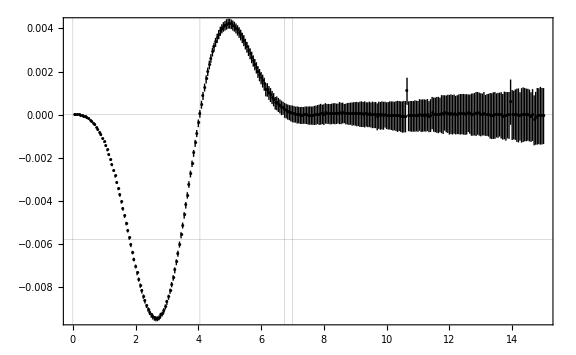

```mathematica
ErrorListPlot[Table[{taberr[[n,1]],ErrorBar[taberr[[n,2]]]},{n,1,Length[taberr]}],GridLines->{{0,4.05,6.75,7},{0,-0.0116,0.0116,-0.0116/2,0.0116/2}},PlotRange->Full,PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{acg}}^{\\circ\\text{ntl}}\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}](*,Epilog->{Inset[Text[MaTeX["\\text{Core}",Magnification->1.25]],{2.25,-0.3}],Inset[Text[MaTeX["\\text{Halo}",Magnification->1.25]],{4.75,0.3}]}*)]
```

```mathematica
taberr[[200]]
```

{{10,-0.0000475661},0.000618733,13.0079}

```mathematica
Total[Transpose[Transpose[taberr][[1]]][[2]]]*1/20
```

-0.0115463

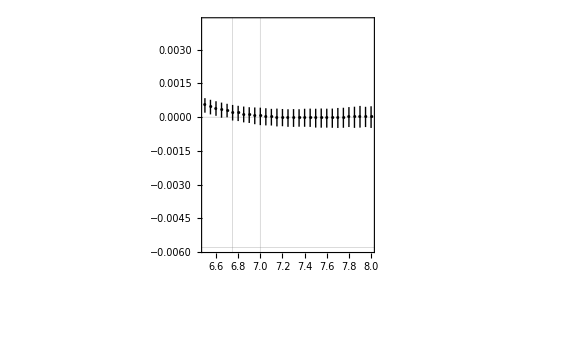

```mathematica
ErrorListPlot[Table[{taberr[[n,1]],ErrorBar[taberr[[n,2]]]},{n,1,Length[taberr]}],GridLines->{{0,4.05,6.75,7},{0,-0.0116,0.0116,-0.0116/2,0.0116/2}},PlotRange->{{6.5,8},Automatic},PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{acg}}^{\\circ\\text{ntl}}\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}](*,Epilog->{Inset[Text[MaTeX["\\text{Core}",Magnification->1.25]],{2.25,-0.3}],Inset[Text[MaTeX["\\text{Halo}",Magnification->1.25]],{4.75,0.3}]}*)]
```

```mathematica
N[taberr[[135]]]
```

{{6.75,0.000199136},0.000346526,1.74014}

```mathematica
Total[Transpose[Take[Transpose[taberr][[1]],120]][[2]]]*1/20
```

-0.0120888

```mathematica
taberr[[140]]
```

{{7,0.000034889},0.000388593,11.138}

```mathematica
Total[Transpose[Take[Transpose[taberr][[1]],140]][[2]]]*1/20
```

-0.0114968

```mathematica
Total[Transpose[Transpose[taberr][[1]]][[2]]]*1/20
```

```mathematica
ft={{-1/10000,"-10 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{-1/20000,"-5 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{-3/10000,"-15 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{1/50000,"",{0.005,0}},{1/100000,"",{0.005,0}},{0,"",{0.005,0}},{-1/100000,"",{0.005,0}},{-1/50000,"",{0.005,0}},{0,"0"},{-3/100000,"",{0.005,0}},{-1/25000,"",{0.005,0}},{-1/20000,"",{0.005,0}},{-3/50000,"",{0.005,0}},{-7/100000,"",{0.005,0}},{-1/12500,"",{0.005,0}},{-9/100000,"",{0.005,0}},{-1/10000,"",{0.005,0}},{-11/100000,"",{0.005,0}},{-3/25000,"",{0.005,0}},{-13/100000,"",{0.005,0}},{-7/50000,"",{0.005,0}},{-3/20000,"",{0.005,0}}};
```

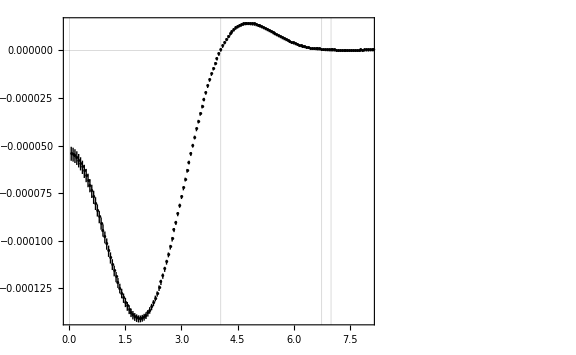

```mathematica
figscgr20thszerothorderdensity=ErrorListPlot[Table[{{taberr[[n,1,1]],taberr[[n,1,2]]/(4*π*taberr[[n,1,1]]^2)},ErrorBar[taberr[[n,2]]/(4*π*taberr[[n,1,1]]^2)]},{n,1,Length[taberr]}],GridLines->{{0,4.05,6.75,7},{0}},(*GridLinesStyle->Directive[Gray],*)PlotRange->{{Automatic,8},Full},PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\frac{\\hat{S}_{\\text{acg}}^{\\circ\\text{ntl}}\\left(k_{\\text{J}}\\beta\\, r\\right)}{4\\pi \\left(k_{\\text{J}}\\beta\\, r\\right)^2}",Magnification->1.25]},RotateLabel->False,
FrameTicks->{{ft,None},{Automatic,None}},ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}](*,Epilog->{Inset[Text[MaTeX["\\text{Core}",Magnification->1.25]],{1.75,-0.0075}],Inset[Text[MaTeX["\\text{Halo}",Magnification->1.25]],{4.4,0.0015}]}*)]
```

```mathematica
Export["figscgr20thszerothorder.pdf",figscgr20thszerothorder,ImageResolution->1000];
```

```mathematica
Export["figscgr20thszerothorderdensity.pdf",figscgr20thszerothorderdensity,ImageResolution->1000];
```

```mathematica
(*Export["2017-05-29 New distribution over space 20ths zeroth order.m",taberr]*)
```

2017-05-29 New distribution over space 20ths zeroth order.m

```mathematica
w0d3[z_]:=(Sin[z]-z*Cos[z])/z^3
```

```mathematica
Clear[r]
```

```mathematica
r^3*w0d3[r*k0]
```

(-k0 r Cos[k0 r]+Sin[k0 r])/k0^3

```mathematica
inter0[r_]:=Module[{int,errors},int=Chop[NIntegrate[Boole[(k1^2+k2^2+2*k1*k2*cth≤1)&&(k1^2+k0^2+2*k1*k0*cpsi≤1)]*k0^2*k1^2*k2^2*r^3*w0d3[r*k0]*term,{k1,0,2},{k2,0,1},{k0,0,3},{ϕ,0,2*π},{cth,-1,1},{cpsi,-1,1},PrecisionGoal->5,(*WorkingPrecision->15,*)IntegrationMonitor:>((errors=Through[#1@"Error"])&)]];
{{r,int/(2*π^2)},Re[Total@errors]/(2*π^2),Abs[Re[Total@errors]/Re[int]]}]
```

```mathematica
late=inter0[15]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.22836+1.74713×10^-63 ⅈ and 0.0379318 for the integral and error estimates.

{{15,-0.0115688},0.00192165,0.166105}

```mathematica
taberr0={};Monitor[For[r=1,r≤15,r=r+1,taberr0=Join[taberr0,{inter0[r]}]],taberr0//MatrixForm//ScientificForm];taberr0//MatrixForm//ScientificForm
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00702256 and 0.000265345 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0838266 and 0.00154058 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.257984 and 0.00338442 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

({1,-3.55767×10^-4} | 1.34425×10^-5 | 3.77846×10^-2
{2,-4.24671×10^-3} | 7.80468×10^-5 | 1.83782×10^-2
{3,-1.30696×10^-2} | 1.71457×10^-4 | 1.31187×10^-2
{4,-1.79985×10^-2} | 2.34106×10^-4 | 1.3007×10^-2
{5,-1.52706×10^-2} | 3.2456×10^-4 | 2.12539×10^-2
{6,-1.21141×10^-2} | 4.42298×10^-4 | 3.65109×10^-2
{7,-1.1419×10^-2} | 5.06307×10^-4 | 4.43389×10^-2
{8,-1.14777×10^-2} | 7.01047×10^-4 | 6.10788×10^-2
{9,-1.14485×10^-2} | 8.2218×10^-4 | 7.18153×10^-2
{10,-1.14407×10^-2} | 9.24687×10^-4 | 8.08244×10^-2
{11,-1.13548×10^-2} | 1.1288×10^-3 | 9.94122×10^-2
{12,-1.15222×10^-2} | 1.24676×10^-3 | 1.08205×10^-1
{13,-1.16281×10^-2} | 1.42403×10^-3 | 1.22464×10^-1
{14,-1.14829×10^-2} | 1.75004×10^-3 | 1.52404×10^-1
{15,-1.15688×10^-2} | 1.92165×10^-3 | 1.66105×10^-1)

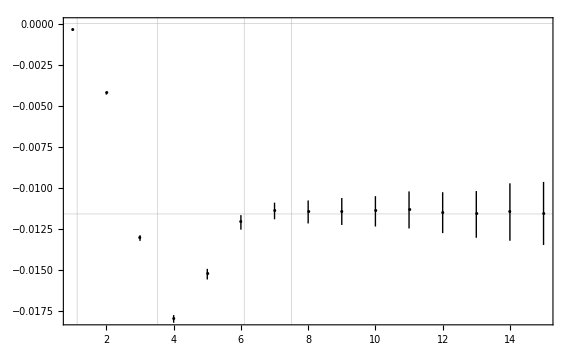

```mathematica
ErrorListPlot[Table[{taberr0[[n,1]],ErrorBar[taberr0[[n,2]]]},{n,1,Length[taberr0]}],GridLines->{{0,1.13,3.525,6.1,7.5},{0,-0.0116}},PlotRange->Full,PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\int_0^{k_{\\text{J}}\\beta\\, r}\\hat{S}_{\\text{acg},r}^\\text{\\,ntl}\\left(r'\\right)\\,\\text{d}r'",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}](*,Epilog->{Inset[Text[MaTeX["\\text{Core}",Magnification->1.25]],{2.25,-0.3}],Inset[Text[MaTeX["\\text{Halo}",Magnification->1.25]],{4.75,0.3}]}*)]
```

```mathematica
interalt[r_]:=Module[{int,errors},int=Chop[NIntegrate[Boole[(k1^2+k2^2+2*k1*k2*cth≤1)(*&&(k1^2+k0^2+2*k1*k0*cpsi≤1)*)]*k0*k1^2*k2^2*r*Sin[r*k0]*term,{k1,0,2},{k2,0,1},{k0,0,3},{ϕ,0,2*π},{cth,-1,1},{cpsi,-1,1},PrecisionGoal->5,(*WorkingPrecision->15,*)IntegrationMonitor:>((errors=Through[#1@"Error"])&)]];
{{r,int/(2*π^2)},Re[Total@errors]/(2*π^2),Abs[Re[Total@errors]/Re[int]]}]
```

```mathematica
taberralt={};Monitor[For[r=1,r≤15,r=r+1,taberralt=Join[taberralt,{interalt[r]}]]
,taberralt//MatrixForm//ScientificForm];taberralt//MatrixForm//ScientificForm
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.20507 and 0.0160498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.60996 and 0.045232 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.919549 and 0.0773642 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

({1,-6.10498×10^-2} | 8.13093×10^-4 | 1.33185×10^-2
{2,8.15616×10^-2} | 2.29148×10^-3 | 2.80951×10^-2
{3,-4.65849×10^-2} | 3.91932×10^-3 | 8.41329×10^-2
{4,7.10501×10^-2} | 6.08945×10^-3 | 8.57064×10^-2
{5,-4.75443×10^-2} | 8.62405×10^-3 | 1.8139×10^-1
{6,4.79896×10^-2} | 1.18653×10^-2 | 2.47248×10^-1
{7,-3.94082×10^-2} | 1.5281×10^-2 | 3.87762×10^-1
{8,3.03461×10^-2} | 1.71381×10^-2 | 5.64754×10^-1
{9,-2.20448×10^-2} | 2.48103×10^-2 | 1.12545
{10,1.16628×10^-2} | 2.72815×10^-2 | 2.3392
{11,-4.92987×10^-3} | 3.03186×10^-2 | 6.14998
{12,-1.48448×10^-2} | 3.5023×10^-2 | 2.35927
{13,2.48023×10^-2} | 2.95455×10^-2 | 1.19124
{14,-2.90417×10^-2} | 4.63646×10^-2 | 1.59648
{15,3.14728×10^-2} | 5.44479×10^-2 | 1.73)

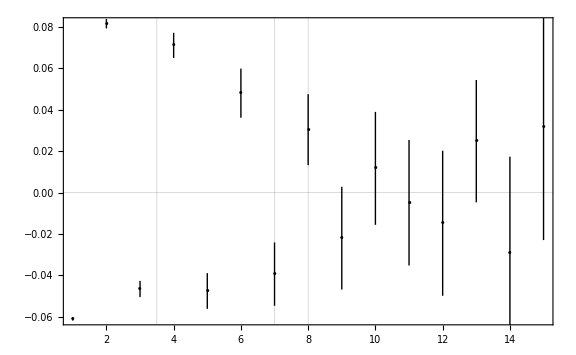

```mathematica
ErrorListPlot[Table[{taberralt[[n,1]],ErrorBar[taberralt[[n,2]]]},{n,1,Length[taberralt]}],GridLines->{{0,3.5,7,8},{0}},PlotRange->Full,PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{cg},r}\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}]]
```

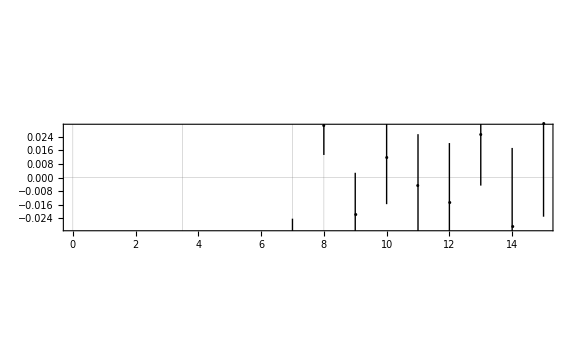

```mathematica
ErrorListPlot[Table[{taberralt[[n,1]],ErrorBar[taberralt[[n,2]]]},{n,1,Length[taberralt]}],GridLines->{{0,3.5,7,8},{0}},PlotRange->{Automatic,{-.03,.03}},PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{cg},r}\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}]]
```